```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
checkers=Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
grid={EdgeForm[{Thin}],FaceForm[Transparent],#}&/@checkers;
blacks=Take[checkers,{1,-1,2}];
whites={White,#}&/@Drop[checkers,{1,-1,2}];
```

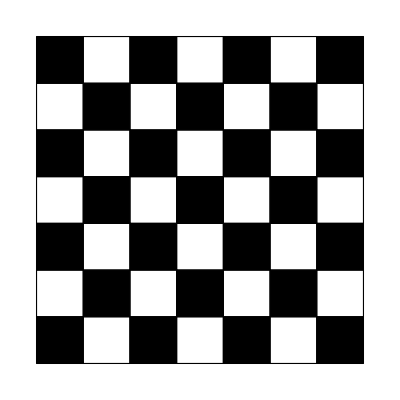

```mathematica
Graphics@{grid,blacks}
```

```mathematica
Export["Checkerboard.png",Graphics@{grid,blacks}]
```

Checkerboard.png

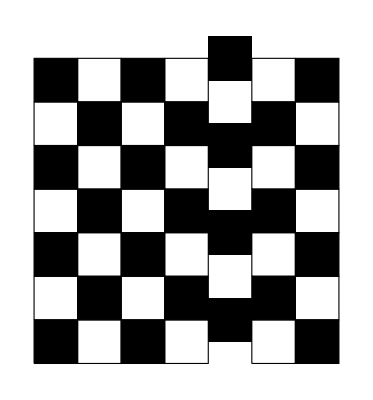

CheckerboardAperiodic.png

```mathematica
newgrid=Complement[grid,Cases[grid,{EdgeForm[{Thickness[Tiny]}],FaceForm[-Graphics-],Translate[Rectangle[{0,0}],{4,_}]}]];
Translate[#,{0,0.5}]&/@Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]];
Complement[blacks,Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]]];
Graphics[{newgrid,%%,%}]
Export["CheckerboardAperiodic.png",%]
```

```mathematica
Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
newblacks=Take[%,{1,-1,3}];
```

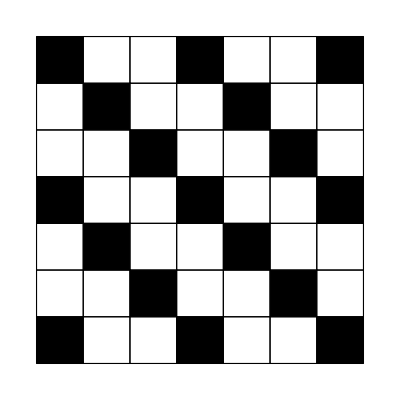

CheckerboardOther.png

```mathematica
Graphics@{grid,newblacks}
Export["CheckerboardOther.png",%]
```

```mathematica
circles=Flatten[Table[Translate[Disk[],{i,j}],{i,0,7,2},{j,0,7,2}],1];
```

```mathematica
Rotate[Graphics[{FaceForm[Black],#}&/@circles],Pi/4];
Graphics[Rotate[circles,Pi/4]]
Table[Graphics[Translate[Rotate[circles,Pi/4],{0,i*2Sqrt[2]}]],{i,-2,1}];
Show[{%,%%},PlotRange->{{-2.3,8.3},{-3.75,6.85}}]
Export["CheckerboardCircles.png",%]
```

-Graphics-

-Graphics-

CheckerboardCircles.png

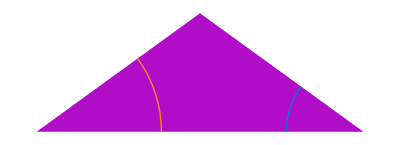

RobinsonFat.png

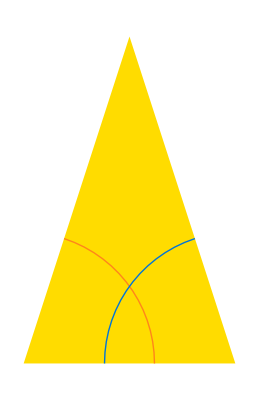

RobinsonSkinny.png

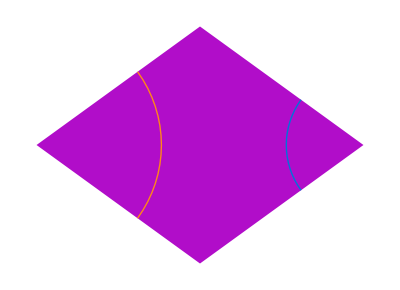

RhombFat.png

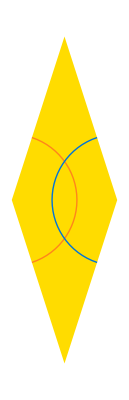

RhombSkinny.png

```mathematica
Show[See@{unitfat},Graphics[MakeCurveRules/@Inflate[{unitfat},0]]]
Export["RobinsonFat.png",%,Background->None,ImageResolution->200]
Show[See@{unitskinny},Graphics[MakeCurveRules/@Inflate[{unitskinny},0]]]
Export["RobinsonSkinny.png",%,Background->None,ImageResolution->200]
Show[See@AddConj@{unitfat},Graphics[MakeCurveRules/@AddConj@Inflate[{unitfat},0]]]
Export["RhombFat.png",%,Background->None,ImageResolution->200]
Show[See@AddConj@{unitskinny},Graphics[MakeCurveRules/@AddConj@Inflate[{unitskinny},0]]]
Export["RhombSkinny.png",%,Background->None,ImageResolution->200]
```

```mathematica
rhombfatunit=Rotate[Polygon/@Coor/@First/@Rhomb/@{unitfat},Pi/5];
rhombskinnyunit=Rotate[Polygon/@Coor/@First/@Rhomb/@{unitskinny},2Pi/5];

rhombfatgrid=Flatten[Table[Translate[rhombfatunit,{i,j}],{i,0,6},{j,0,6,2*0.951}],1];
rhombskinnygrid=Translate[Flatten[Table[Translate[rhombskinnyunit,{i,j}],{i,0,6,ϕ},{j,0.951,6,2*0.951}],1],{0.8,0}];

fatrules=Rotate[MakeCurveRules/@AddConj@Inflate[{unitfat},0],Pi/5];
fatrulesgrid=Flatten[Table[Translate[fatrules,{i,j}],{i,0,6},{j,0,6,2*0.951}],1];

skinnyrules=Rotate[MakeCurveRules/@AddConj@Inflate[{unitskinny},0],2Pi/5];
skinnyrulesgrid=Translate[Flatten[Table[Translate[skinnyrules,{i,j}],{i,0,6,ϕ},{j,0.951,6,2*0.951}],1],{0.8,0}];

Show[Graphics[{FaceForm[None],EdgeForm[Black],rhombfatgrid}],
Graphics[{FaceForm[None],EdgeForm[Black],rhombskinnygrid}],PlotRange->{{-1,7.3},{-0.6,6.5}}]
Export["RhombPeriodic.png",%,Background->None,ImageResolution->200]

Show[Graphics[{FaceForm[None],EdgeForm[Black],rhombfatgrid}],
Graphics[{FaceForm[None],EdgeForm[Black],rhombskinnygrid}],Graphics[fatrulesgrid],Graphics[skinnyrulesgrid],PlotRange->{{-1,7.3},{-0.6,6.5}}]
Export["RhombPeriodicRules.png",%,Background->None,ImageResolution->200]
```

-Graphics-

RhombPeriodic.png

-Graphics-

RhombPeriodicRules.png

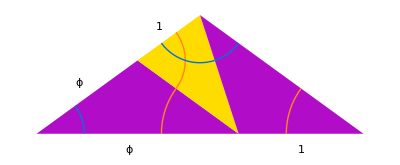

RobFatSub.png

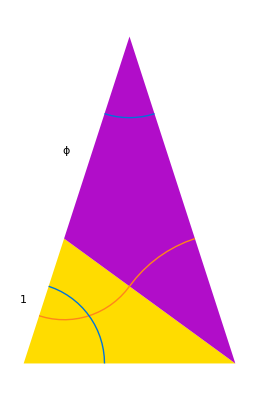

RobSkinnySub.png

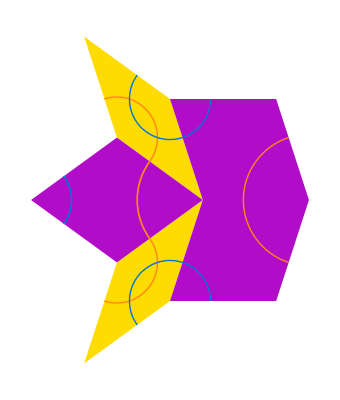

RhombFatSub.png

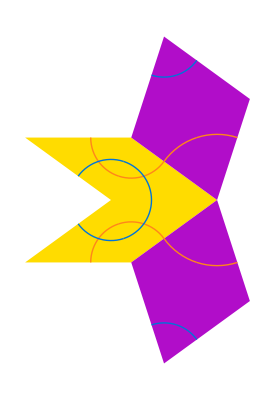

RhombSkinnySub.png

RobFatSub.png

-Graphics-

RobSkinnySub.png

-Graphics-

RhombFatSub.png

-Graphics-

RhombSkinnySub.png

```mathematica
Show[See@Inflate[{unitfat},1],Graphics[MakeCurveRules/@Inflate[{unitfat},1]],Graphics[Text[Style["ϕ",Large],{-0.6,0.25}]],Graphics[Text[Style["1",Large],{-0.2,0.53}]],Graphics[Text[Style["ϕ",Large],{-0.35,-0.08}]],Graphics[Text[Style["1",Large],{0.5,-0.08}]]]
Export["RobFatSub.png",%,Background->None,ImageResolution->200]
Show[See@Inflate[{unitskinny},1],Graphics[MakeCurveRules/@Inflate[{unitskinny},1]],Graphics[Text[Style["ϕ",Large],{-0.3,1}]],Graphics[Text[Style["1",Large],{-0.5,0.3}]]]
Export["RobSkinnySub.png",%,Background->None,ImageResolution->200]
Show[See@FullInflate[{unitfat},1],Graphics[MakeCurveRules/@AddConj@AddRhombTris@Inflate[{unitfat},1]]]
Export["RhombFatSub.png",%,Background->None,ImageResolution->200]
Show[See@FullInflate[{unitskinny},1],Graphics[MakeCurveRules/@AddConj@AddRhombTris@Inflate[{unitskinny},1]]]
Export["RhombSkinnySub.png",%,Background->None,ImageResolution->200]
```

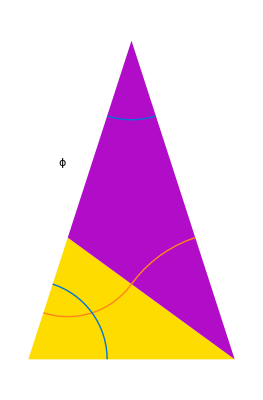

```mathematica
Show[See@FullInflate[starseed,6]]
```

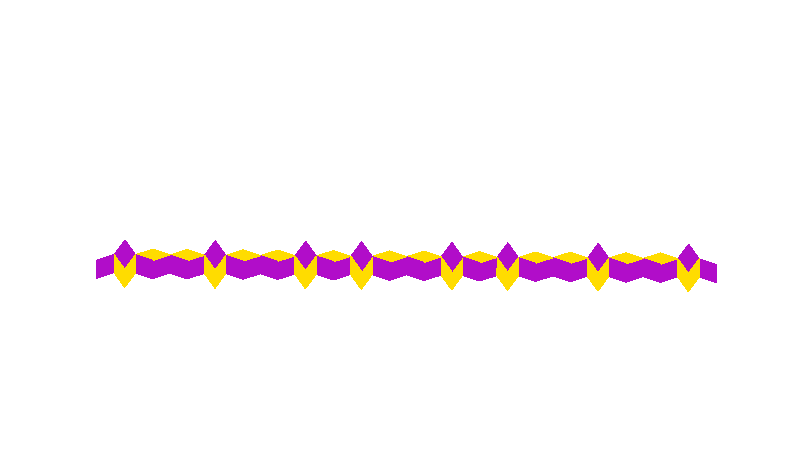

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0730658003275355,0.46395030173298013],List[1.0726551073229873,0.4082237250715891],List[1.125527320069748,0.3906126735867088],List[1.1259380130742964,0.44633925024809973]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0406427980253743,0.5092754485816768],List[1.0075552804829124,0.4644331003155664],List[1.0399782827850736,0.4191079534668697],List[1.0730658003275355,0.46395030173298013]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.072655107322987,0.4082237250715893],List[1.0395675897805252,0.3633813768054789],List[1.0399782827850736,0.4191079534668697],List[1.0730658003275355,0.46395030173298013]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0075552804829124,0.4644331003155664],List[0.954429245500399,0.44760323334703084],List[0.9540185524958507,0.39187665668563987],List[1.0071445874783642,0.4087065236541755]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.0071445874783642,0.4087065236541755],List[1.0395675897805252,0.3633813768054788],List[1.0399782827850736,0.4191079534668697],List[1.0075552804829124,0.4644331003155664]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.954429245500399,0.4476032333470307],List[0.9015570327536381,0.4652142848319112],List[0.9546830677361515,0.4820441518004469],List[1.0075552804829124,0.4644331003155664]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901557032753638,0.4652142848319112],List[0.9011463397490899,0.4094877081705204],List[0.9540185524958507,0.39187665668563987],List[0.954429245500399,0.4476032333470307]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901557032753638,0.4652142848319112],List[0.8484309977711244,0.4483844178633756],List[0.8480203047665762,0.39265784120198477],List[0.9011463397490899,0.4094877081705204]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.8484309977711245,0.44838441786337546],List[0.7955587850243636,0.46599546934825586],List[0.8486848200068771,0.4828253363167916],List[0.901557032753638,0.4652142848319112]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7955587850243635,0.465995469348256],List[0.7951480920198153,0.4102688926868653],List[0.8480203047665762,0.39265784120198477],List[0.8484309977711245,0.44838441786337546]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7631357827222025,0.5113206161969527],List[0.7300482651797406,0.46647826793084207],List[0.7624712674819016,0.42115312108214553],List[0.7955587850243635,0.465995469348256]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7951480920198154,0.41026889268686506],List[0.7620605744773534,0.3654265444207546],List[0.7624712674819016,0.42115312108214553],List[0.7955587850243635,0.465995469348256]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7300482651797406,0.46647826793084224],List[0.6769222301972271,0.4496484009623066],List[0.6765115371926789,0.3939218243009157],List[0.7296375721751924,0.4107516912694513]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7296375721751924,0.4107516912694513],List[0.7620605744773534,0.3654265444207546],List[0.7624712674819016,0.42115312108214553],List[0.7300482651797406,0.46647826793084224]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6769222301972271,0.4496484009623065],List[0.6240500174504662,0.4672594524471871],List[0.6771760524329796,0.48408931941572275],List[0.7300482651797406,0.46647826793084224]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6240500174504662,0.4672594524471871],List[0.623639324445918,0.4115328757857961],List[0.6765115371926789,0.3939218243009157],List[0.6769222301972271,0.4496484009623065]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6240500174504662,0.4672594524471871],List[0.5709239824679526,0.45042958547865136],List[0.5705132894634044,0.3947030088172606],List[0.623639324445918,0.4115328757857961]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5709239824679526,0.45042958547865136],List[0.5180517697211917,0.4680406369635318],List[0.5711778047037053,0.48487050393206754],List[0.6240500174504662,0.4672594524471871]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.5180517697211917,0.46804063696353193],List[0.5176410767166435,0.4123140603021411],List[0.5705132894634044,0.3947030088172606],List[0.5709239824679526,0.45042958547865136]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4856287674190306,0.5133657838122285],List[0.45254124987656885,0.46852343554611803],List[0.4849642521787299,0.4231982886974215],List[0.5180517697211917,0.46804063696353193]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5176410767166435,0.412314060302141],List[0.48455355917418175,0.36747171203603046],List[0.4849642521787299,0.4231982886974215],List[0.5180517697211917,0.46804063696353193]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.45254124987656874,0.46852343554611814],List[0.3994152148940553,0.4516935685775824],List[0.3990045218895071,0.39596699191619156],List[0.45213055687202064,0.41279685888472717]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.45213055687202064,0.41279685888472717],List[0.45254124987656885,0.46852343554611803],List[0.4849642521787299,0.4231982886974215],List[0.4845535591741817,0.3674717120360306]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3994152148940553,0.4516935685775824],List[0.3465430021472944,0.4693046200624629],List[0.39966903712980784,0.4861344870309986],List[0.45254124987656874,0.46852343554611814]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34654300214729433,0.4693046200624629],List[0.3461323091427462,0.41357804340107196],List[0.3990045218895071,0.39596699191619156],List[0.3994152148940553,0.4516935685775824]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3461323091427462,0.41357804340107196],List[0.3130447916002843,0.3687356951349616],List[0.31345548460483247,0.42446227179635254],List[0.34654300214729433,0.4693046200624629]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3141199998451333,0.5146297669111595],List[0.28103248230267136,0.4697874186450491],List[0.31345548460483247,0.42446227179635254],List[0.34654300214729433,0.4693046200624629]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.28103248230267136,0.4697874186450491],List[0.22790644732015786,0.45295755167651336],List[0.22749575431560964,0.3972309750151226],List[0.2806217892981232,0.4140608419836582]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2806217892981232,0.4140608419836582],List[0.28103248230267136,0.4697874186450492],List[0.31345548460483247,0.42446227179635254],List[0.3130447916002843,0.3687356951349616]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.22790644732015786,0.4529575516765134],List[0.1750342345733969,0.47056860316139393],List[0.22816026955591046,0.4873984701299296],List[0.28103248230267136,0.4697874186450491]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.1750342345733969,0.47056860316139393],List[0.1746235415688487,0.414842026500003],List[0.22749575431560964,0.3972309750151226],List[0.22790644732015786,0.4529575516765134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.1750342345733969,0.47056860316139393],List[0.12190819959088336,0.4537387361928582],List[0.12149750658633518,0.3980121595314673],List[0.1746235415688487,0.414842026500003]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12190819959088339,0.45373873619285815],List[0.06903598684412243,0.47134978767773866],List[0.12216202182663596,0.48817965464627444],List[0.1750342345733969,0.47056860316139393]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.06903598684412246,0.4713497876777386],List[0.0686252938395743,0.4156232110163477],List[0.12149750658633518,0.3980121595314673],List[0.12190819959088339,0.45373873619285815]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0686252938395743,0.4156232110163478],List[0.03553777629711241,0.37078086275023736],List[0.035948469301660596,0.4265074394116283],List[0.06903598684412246,0.4713497876777386]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.03661298454196138,0.5166749345264352],List[0.0035254669994994603,0.47183258626032487],List[0.035948469301660596,0.4265074394116283],List[0.06903598684412246,0.4713497876777386]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003525466999499488,0.4718325862603248],List[-0.04960056798301404,0.4550027192917891],List[-0.05001126098756223,0.39927614263039823],List[0.003114773994951331,0.41610600959893407]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.003114773994951331,0.41610600959893407],List[0.0035254669994994603,0.47183258626032487],List[0.035948469301660596,0.4265074394116283],List[0.035537776297112356,0.37078086275023736]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.049600567983014016,0.4550027192917891],List[-0.10247278072977489,0.47261377077666966],List[-0.04934674574726139,0.48944363774520533],List[0.003525466999499488,0.4718325862603248]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10247278072977495,0.47261377077666955],List[-0.10288347373432316,0.41688719411527864],List[-0.05001126098756223,0.39927614263039823],List[-0.049600567983014016,0.4550027192917891]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.13489578303193606,0.5179389176253661],List[-0.16798330057439792,0.47309656935925576],List[-0.1355602982722368,0.4277714225105592],List[-0.10247278072977495,0.47261377077666955]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10288347373432316,0.41688719411527875],List[-0.13597099127678502,0.3720448458491683],List[-0.1355602982722368,0.4277714225105592],List[-0.10247278072977495,0.47261377077666955]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16798330057439786,0.47309656935925576],List[-0.22110933555691137,0.45626670239072],List[-0.22152002856145953,0.4005401257293292],List[-0.16839399357894608,0.417369992697865]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.16839399357894608,0.417369992697865],List[-0.13597099127678502,0.3720448458491683],List[-0.1355602982722368,0.4277714225105592],List[-0.16798330057439786,0.47309656935925576]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.22110933555691137,0.4562667023907201],List[-0.27398154830367216,0.47387775387560055],List[-0.22085551332115877,0.4907076208441362],List[-0.16798330057439786,0.47309656935925576]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.2739815483036723,0.4738777538756005],List[-0.27439224130822054,0.4181511772142096],List[-0.22152002856145953,0.4005401257293292],List[-0.22110933555691137,0.4562667023907201]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.2739815483036723,0.4738777538756005],List[-0.32710758328618583,0.4570478869070649],List[-0.32751827629073405,0.40132131024567397],List[-0.27439224130822054,0.4181511772142096]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32710758328618583,0.4570478869070649],List[-0.37997979603294674,0.4746589383919454],List[-0.3268537610504333,0.4914888053604811],List[-0.2739815483036723,0.4738777538756005]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.3799797960329466,0.4746589383919454],List[-0.38039048903749495,0.4189323617305545],List[-0.32751827629073405,0.40132131024567397],List[-0.32710758328618583,0.4570478869070649]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41240279833510773,0.5199840852406421],List[-0.4454903158775696,0.4751417369745316],List[-0.4130673135754086,0.42981659012583495],List[-0.3799797960329466,0.4746589383919454]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38039048903749495,0.4189323617305545],List[-0.4134780065799568,0.37409001346444404],List[-0.4130673135754086,0.42981659012583495],List[-0.3799797960329466,0.4746589383919454]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.4454903158775696,0.4751417369745316],List[-0.49861635086008316,0.45831187000599594],List[-0.49902704386463137,0.402585293344605],List[-0.4459010088821179,0.41941516031314074]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4459010088821179,0.41941516031314074],List[-0.4134780065799568,0.37409001346444404],List[-0.4130673135754086,0.42981659012583495],List[-0.4454903158775696,0.4751417369745316]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.49861635086008316,0.45831187000599594],List[-0.5514885636068441,0.4759229214908764],List[-0.4983625286243305,0.49275278845941206],List[-0.4454903158775696,0.4751417369745316]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5514885636068441,0.4759229214908764],List[-0.5518992566113924,0.42019634482948554],List[-0.49902704386463137,0.402585293344605],List[-0.49861635086008316,0.45831187000599594]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5514885636068441,0.4759229214908764],List[-0.6046145985893577,0.4590930545223407],List[-0.6050252915939058,0.4033664778609499],List[-0.5518992566113924,0.42019634482948554]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6046145985893576,0.4590930545223407],List[-0.6574868113361186,0.47670410600722124],List[-0.604360776353605,0.4935339729757569],List[-0.5514885636068441,0.4759229214908764]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6574868113361185,0.47670410600722124],List[-0.6578975043406667,0.4209775293458303],List[-0.6050252915939058,0.4033664778609499],List[-0.6046145985893576,0.4590930545223407]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6899098136382796,0.5220292528559178],List[-0.7229973311807415,0.4771869045898074],List[-0.6905743288785804,0.4318617577411107],List[-0.6574868113361185,0.47670410600722124]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6578975043406667,0.4209775293458303],List[-0.6909850218831286,0.3761351810797199],List[-0.6905743288785804,0.4318617577411107],List[-0.6574868113361185,0.47670410600722124]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.7229973311807415,0.4771869045898074],List[-0.7761233661632551,0.46035703762127167],List[-0.7765340591678032,0.40463046095988087],List[-0.7234080241852896,0.4214603279284165]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.7234080241852896,0.4214603279284165],List[-0.6909850218831285,0.3761351810797199],List[-0.6905743288785804,0.4318617577411107],List[-0.7229973311807415,0.4771869045898074]]]]],Rule[ImageMargins,0.],Rule[ImagePadding,List[List[0.,0.625],List[0.625,0.]]],Rule[ImageSize,List[800.374999999993,Automatic]],Rule[PlotRange,List[List[-0.849163889856715,1.1581808842316623],List[-0.038541019662496845,1.1283548116705382]]],Rule[PlotRangePadding,Automatic]]
```

-Graphics-

```mathematica
automaton=({{"B"->"A'","α'"},{"A'"->"A'","β'"},{"A'"->"B'","δ"},{"B'"->"B'","ϵ"},{"B'"->"A","α"},{"A"->"A","β"},{"A"->"B","δ'"},{"B"->"B","ϵ'"}, {"B"->"B'","γ"},{"B'"->"B","γ'"}}/.Rule->DirectedEdge)/.{"B"->"T'","B'"->"T","A"->"t","A'"->"t'"}
names={"A","B'","A'","B"}/.{"B"->"T","B'"->"T'","A"->"t","A'"->"t'"}
```

{{T'->t',α'},{t'->t',β'},{t'->T,δ},{T->T,ϵ},{T->t,α},{t->t,β},{t->T',δ'},{T'->T',ϵ'},{T'->T,γ},{T->T',γ'}}

{t,T',t',T}

```mathematica
vertexrules=MapThread[Rule[#1,Placed[#1,#2]]&,{names,{{Before},{Above},{After},{Below}}}]
```

{t→Placed[t,{Before}],T'→Placed[T',{Above}],t'→Placed[t',{After}],T→Placed[T,{Below}]}

```mathematica
Graph[MapThread[Labeled,{automaton[[All,1]],automaton[[All,2]]}], VertexLabels->vertexrules, VertexLabelStyle->Directive[20], EdgeLabelStyle->Directive[20],GraphStyle->"BasicBlack"]
```

-Graphics-

```mathematica
Edg
```

```mathematica
automaton[[All,1]]
```

{B→A',A'→A',A'→B',B'→B',B'→A,A→A,A→B,B→B,B→B',B'→B}

```mathematica
edgerules=MapThread[#1->Graphics[{Table[{Opacity[0.4-1/n],FaceForm[White],Disk[{0,0},1/n]},{n,1,50}],{Text[Style[#2,20, FontFamily->"CMU Serif"]]}}]&,{automaton[[All,1]],automaton[[All,2]],{{Above,After},{After},{Below,After},{Below},{Below,Before},{Before},{Above, Before},{Above},{After},{Before}}}]
```

{T'->t'→-Graphics-,t'->t'→-Graphics-,t'->T→-Graphics-,T->T→-Graphics-,T->t→-Graphics-,t->t→-Graphics-,t->T'→-Graphics-,T'->T'→-Graphics-,T'->T→-Graphics-,T->T'→-Graphics-}

```mathematica
Graph[automaton[[All,1]],VertexLabels->vertexrules, EdgeLabels->edgerules,VertexLabelStyle->Directive[20,FontFamily->"CMU Serif"],GraphStyle->"BasicBlack",ImageSize->600]
Export["UpDownGraph.png",%,ImageResolution->300]
```

-Graphics-

UpDownGraph.png

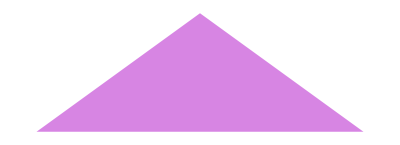

```mathematica
SeeFaded@{unitfat}
```

```mathematica
a1=Graphics[Line[{{{1,1/2},{2,0},{1,-1/2}}}]];
a2=Graphics[Line[{{{0,1/2},{1,0},{0,-1/2}},{{1,1/2},{2,0},{1,-1/2}}}]];
a3=Graphics[Line[{{{-1,1/2},{0,0},{-1,-1/2}},{{0,1/2},{1,0},{0,-1/2}},{{1,1/2},{2,0},{1,-1/2}}}]];
```

```mathematica
ArrowEdges[{{A_,B_,C_},T_}]:=
If[T=="fat",
Graphics[{
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]},
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]}
}]&@Coor@{A,B,C},
Graphics[{
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[1]]}]},
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]}
}]&@Coor@{A,B,C}]

SeeFaded:=Graphics[{Opacity[0.3],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&
```

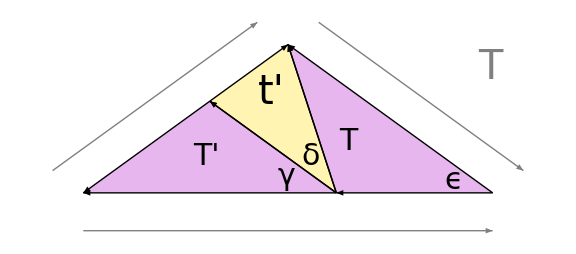

TF.png

```mathematica
Show[SeeFaded@Inflate[{unitfat},1],ArrowEdges/@Inflate[{unitfat},1],
Graphics[Text[Style["γ",30, FontFamily->"CMU Serif"],{-0.005852264137550245,0.07022716965060338}]],Graphics[Text[Style["δ",30, FontFamily->"CMU Serif"],{0.0907100941320289,0.14903866899467566}]],Graphics[Text[Style["ϵ",30, FontFamily->"CMU Serif"],{0.6554535834056285,0.05247631072509673}]],Graphics[Text[Style["T'",30, FontFamily->"CMU Serif"],{-0.32187452756526413,0.14903866899467522}]],Graphics[Text[Style["t'",40, FontFamily->"CMU Serif"],{-0.0643749055130527,0.4006860269093364}]],Graphics[Text[Style["T",30, FontFamily->"CMU Serif"],{0.23994282963956048,0.2075613103701781}]],
Graphics[{Gray,Text[Style["T",40, FontFamily->"CMU Serif"],{0.8,0.5}]}],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]},0.15(#[[3]]-#[[2]])]&@Coor@Δ@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])]&@Coor@Δ@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,-1})]&@Coor@Δ@unitfat],
ImageSize->Large
]
Export["TF.png",%,ImageResolution->300]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T.png"]]]
```

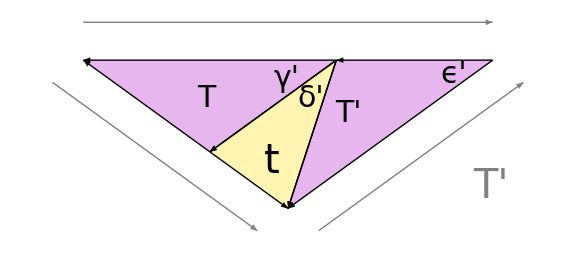

TF'.png

```mathematica
Show[SeeFaded@Inflate[{Conj@unitfat},1],ArrowEdges/@Inflate[{Conj@unitfat},1],
Graphics[Text[Style["γ'",30, FontFamily->"CMU Serif"],{-0.005852264137550245,-0.07022716965060338}]],Graphics[Text[Style["δ'",30, FontFamily->"CMU Serif"],{0.0907100941320289,-0.14903866899467566}]],Graphics[Text[Style["ϵ'",30, FontFamily->"CMU Serif"],{0.6554535834056285,-0.05247631072509673}]],Graphics[Text[Style["T",30, FontFamily->"CMU Serif"],{-0.32187452756526413,-0.14903866899467522}]],Graphics[Text[Style["t",40, FontFamily->"CMU Serif"],{-0.0643749055130527,-0.4006860269093364}]],Graphics[Text[Style["T'",30, FontFamily->"CMU Serif"],{0.23994282963956048,-0.2075613103701781}]],
Graphics[{Gray,Text[Style["T'",40, FontFamily->"CMU Serif"],{0.8,-0.5}]}],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]},0.15(#[[3]]-#[[2]])]&@Coor@Δ@Conj@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])]&@Coor@Δ@Conj@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,1})]&@Coor@Δ@Conj@unitfat],
ImageSize->Large
]
Export["TF'.png",%,ImageResolution->300]
```

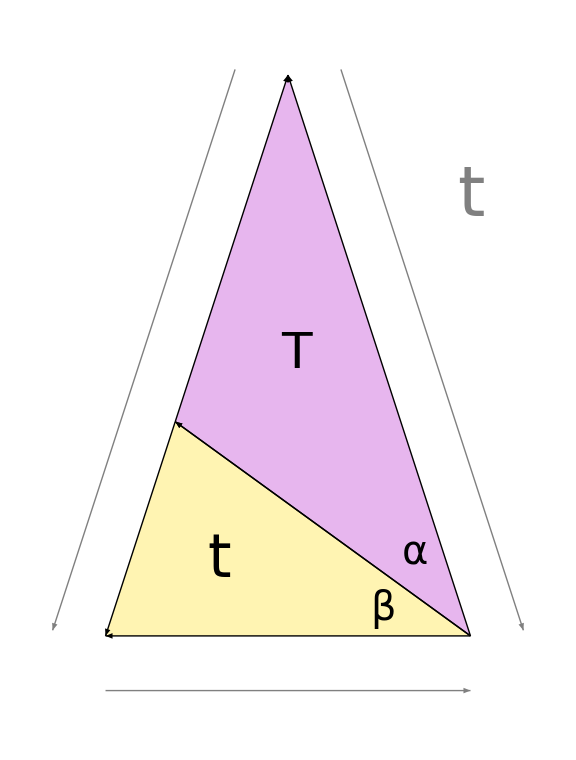

tS.png

```mathematica
Show[SeeFaded@Inflate[{unitskinny},1],ArrowEdges/@Inflate[{unitskinny},1],
Graphics[Text[Style["β",40, FontFamily->"CMU Serif"],{0.25910539662002213,0.07303394842367927}]],Graphics[Text[Style["α",40, FontFamily->"CMU Serif"],{0.34755820241294855,0.22703397043860196}]],Graphics[Text[Style["t",60, FontFamily->"CMU Serif"],{-0.189885164661828,0.2070478594952605}]],Graphics[Text[Style["T",50, FontFamily->"CMU Serif"],{0.021951326907476976,0.7734004519241982}]],
Graphics[{Gray,Text[Style["t",70, FontFamily->"CMU Serif"],{0.5,1.2042972031781072}]}],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[1]]}]},0.15(#[[3]]-#[[2]])],0.14(#[[1]]-#[[3]])]&@Coor@Δ@unitskinny],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])],0.14(#[[2]]-#[[3]])]&@Coor@Δ@unitskinny],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,-1})]&@Coor@Δ@unitskinny],
ImageSize->Large
]
Export["tS.png",%,ImageResolution->300]
```

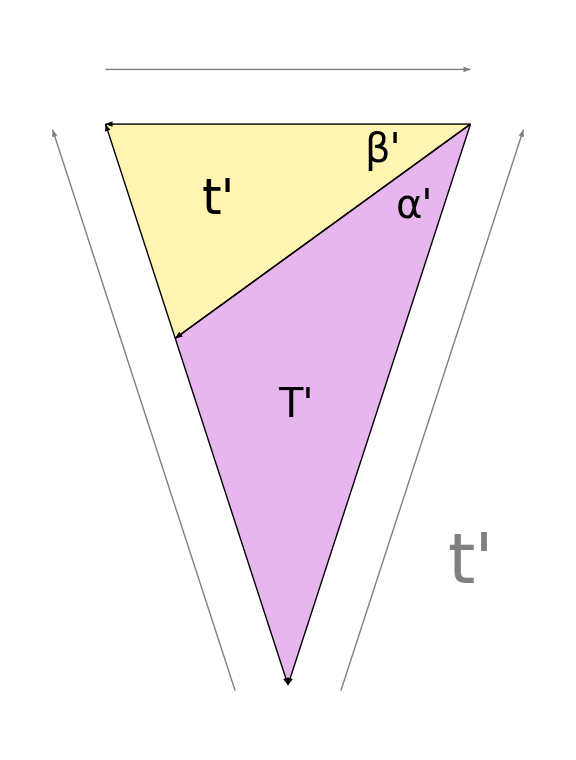

tS'.png

```mathematica
Show[SeeFaded@Inflate[{Conj@unitskinny},1],ArrowEdges/@Inflate[{Conj@unitskinny},1],
Graphics[Text[Style["β'",40, FontFamily->"CMU Serif"],{0.25910539662002213,-0.07303394842367927}]],Graphics[Text[Style["α'",40, FontFamily->"CMU Serif"],{0.34755820241294855,-0.22703397043860196}]],Graphics[Text[Style["t'",50, FontFamily->"CMU Serif"],{-0.189885164661828,-0.2070478594952605}]],Graphics[Text[Style["T'",40, FontFamily->"CMU Serif"],{0.021951326907476976,-0.7734004519241982}]],
Graphics[{Gray,Text[Style["t'",70, FontFamily->"CMU Serif"],{0.5,-1.2042972031781072}]}],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[1]]}]},0.15(#[[3]]-#[[2]])],0.14(#[[1]]-#[[3]])]&@Coor@Δ@Conj@unitskinny],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])],0.14(#[[2]]-#[[3]])]&@Coor@Δ@Conj@unitskinny],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,1})]&@Coor@Δ@Conj@unitskinny],
ImageSize->Large
]
Export["tS'.png",%,ImageResolution->300]
```

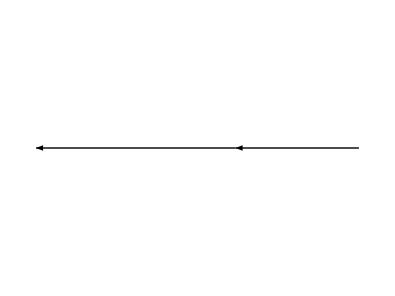
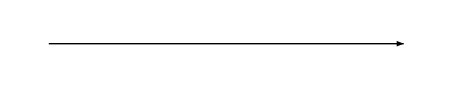
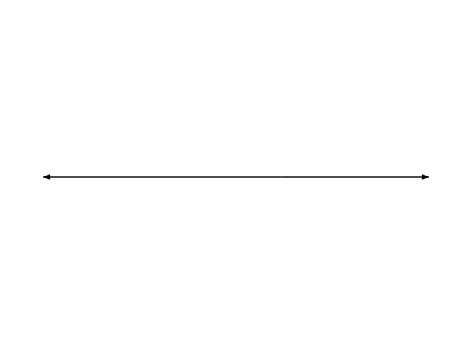
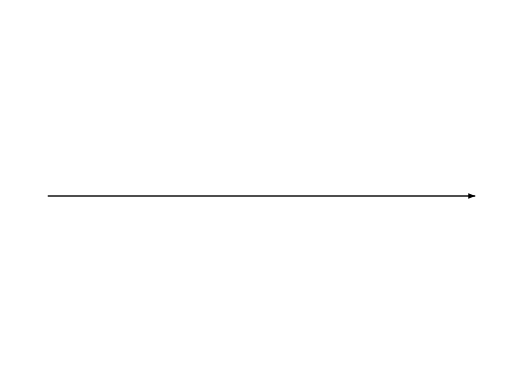
```mathematica
Export["a1inflate.png",-Graphics-,ImageResolution->300]
Export["a1.png",-Graphics-,ImageResolution->300]

Export["a2inflate.png",-Graphics-,ImageResolution->300]
Export["a2.png",-Graphics-,ImageResolution->300]
```

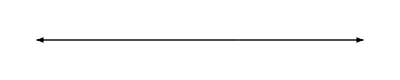

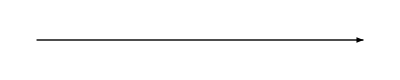

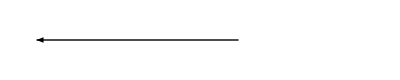

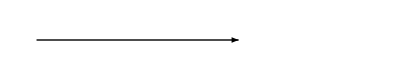

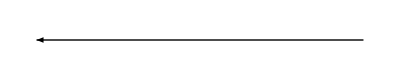

-Graphics-

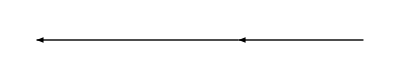

-Graphics-

```mathematica
Graphics[{
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[2]],#[[1]]}]},
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[2]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a1inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a1.png",%,ImageResolution->300];

Graphics[{
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[2]],#[[1]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a2inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a2.png",%,ImageResolution->300];

Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[3]],#[[1]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a3inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[1]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a3.png",%,ImageResolution->300];

Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[2]],#[[1]]}]},
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[2]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a4inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a4.png",%,ImageResolution->300];
```

```mathematica
See@{unitskinny}
```

```mathematica
Graphics[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0],List[0.5,0],List[0.,1.5388417685876268]]]]]
```

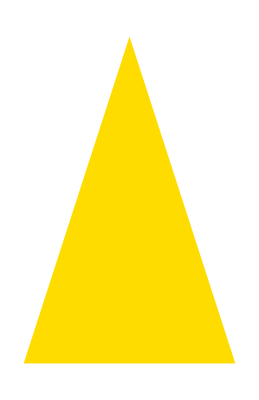

```mathematica
Graphics[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0],List[0.5,0],List[0.,1.5388417685876268]]]]]
```

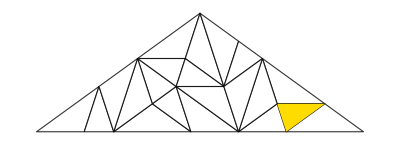

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.8090169943749475,0],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[0.1909830056250527,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]]]]
Export["Down1.png",%,ImageResolution->300];
```

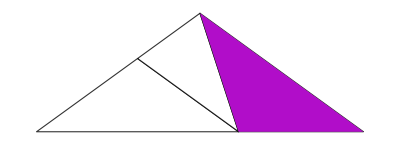

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]
Export["Down1.png",%,ImageResolution->300];
```

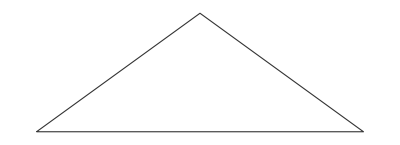

```mathematica
Graphics[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[GrayLevel[1],Polygon[List[List[-0.8090169943749475,0],List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]]]
Export["Down4.png",%,ImageResolution->300];
```

```mathematica
Show[See@Inflate[{unitfat},2],ArrowEdges/@Inflate[{unitfat},2]]
```

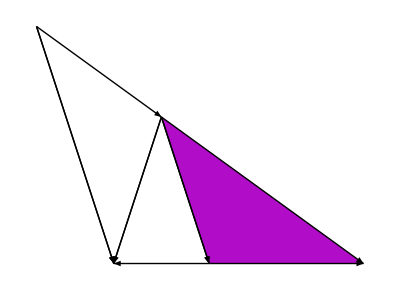

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.42705098312484224,0],List[0.8090169943749475,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.19098300562505244,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.42705098312484224,0],List[0.19098300562505244,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.30901699437494756,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.19098300562505244,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]]
Export["Up3Left.png",%,ImageResolution->300];
```

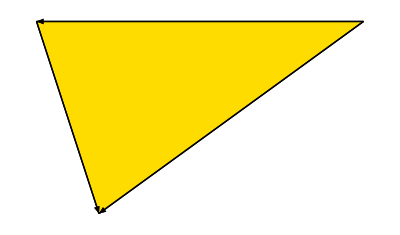
```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]]]]
Export["Up1Left.png",%,ImageResolution->300];
```

-Graphics-

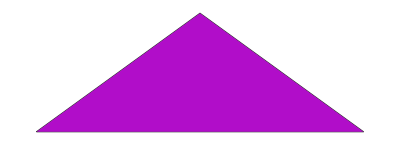

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[GrayLevel[1],Polygon[List[List[-0.8090169943749475,0],List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.8090169943749475,0],List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]]]
Export["Down4.png",%,ImageResolution->300];
```

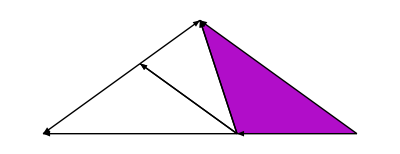
```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[-0.30901699437494745,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[-0.30901699437494745,0.3632712640026805],List[-0.8090169943749475,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[-0.8090169943749475,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[-0.30901699437494745,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[1.1102230246251565*^-16,0.5877852522924732]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[0.19098300562505244,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[1.1102230246251565*^-16,0.5877852522924732]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]]],Rule[ImagePadding,List[List[0.,0.909091],List[0.909091,0.]]],Rule[PlotRange,List[List[-0.8427260358072369,0.8427260358072369],List[-0.032360679774997896,0.6201459320674712]]],Rule[PlotRangePadding,Automatic]]
Export["Up4Left.png",%,ImageResolution->300]
```

-Graphics-

Up4Left.png

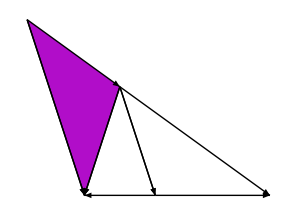
```mathematica
-Graphics-//FullForm
```

-Graphics-

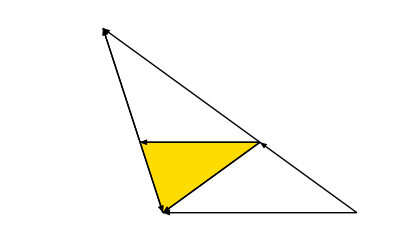

```mathematica
Graphics[List[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.30901699437494756,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[0.6180339887498949,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[0.42705098312484224,0]]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.30901699437494756,0.3632712640026805]]]]],Rule[ImagePadding,List[List[0.,0.909091],List[0.909091,0.]]],Rule[PlotRange,List[List[0.1781072975260963,0.8218927024739036],List[-0.0123606797749979,0.3756319437776784]]],Rule[PlotRangePadding,Automatic]]
Export["Up2Left.png",%,ImageResolution->300];
```

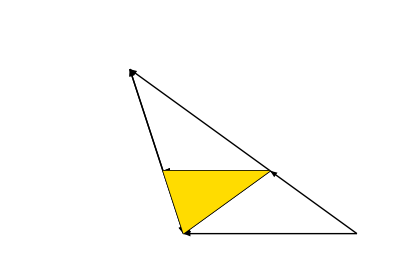

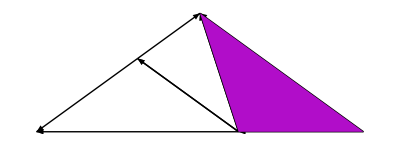

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]
Export["Down3.png",%,ImageResolution->300];
```

-Graphics-

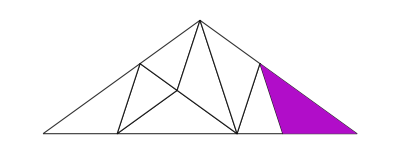

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[-0.42705098312484224,0],List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0]]]],List[GrayLevel[1],Polygon[List[List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0]]]],List[GrayLevel[1],Polygon[List[List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732]]]],List[GrayLevel[1],Polygon[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]],List[GrayLevel[1],Polygon[List[List[0.42705098312484224,0],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]]],Rule[ImagePadding,List[List[0.,0.909091],List[0.909091,0.]]],Rule[PlotRange,List[List[-0.8427260358072369,0.8427260358072369],List[-0.032360679774997896,0.6201459320674712]]],Rule[PlotRangePadding,Automatic]]
Export["Down2.png",%,ImageResolution->300];
```

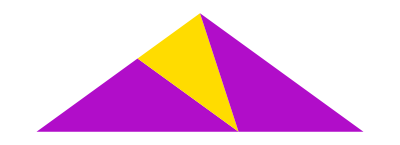

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.19098300562505244,0],List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]
Export["Up4.png",%,ImageResolution->300];
```

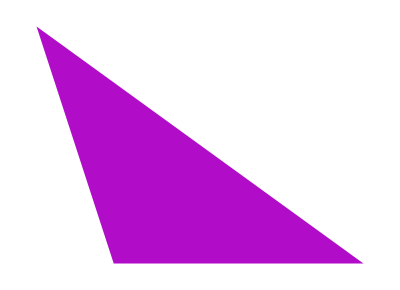

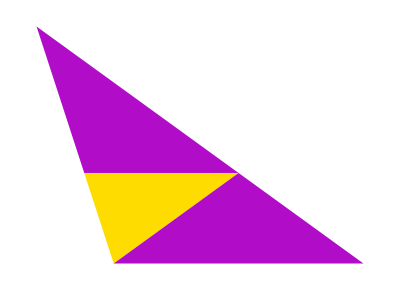

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]]]]
Export["Up2.png",%,ImageResolution->300];
```

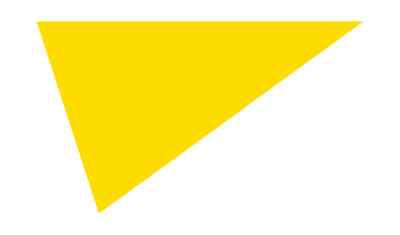

```mathematica
Graphics[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]]]
Export["Up1.png",%,ImageResolution->300];
```

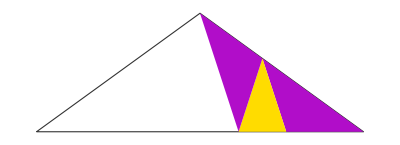

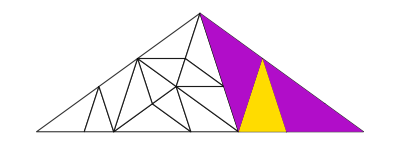
```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.8090169943749475,0],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[0.1909830056250527,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]]]],List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.42705098312484224,0],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]]]]]
Export["Down3.png",%,ImageResolution->300];
```

-Graphics-

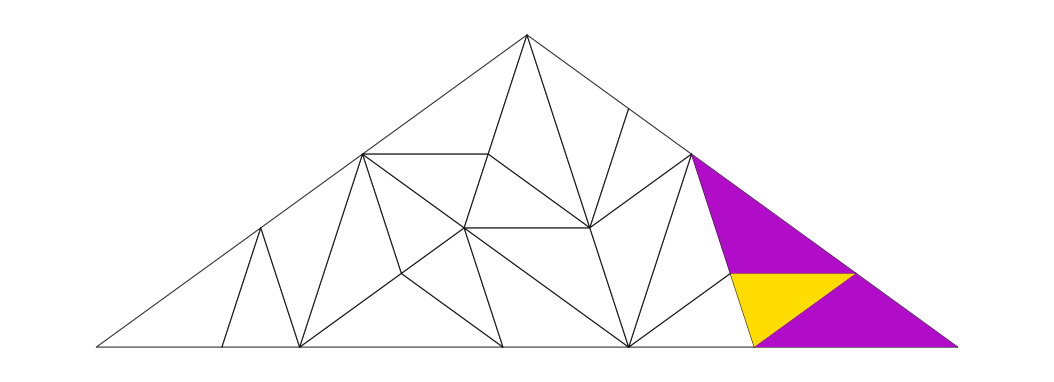

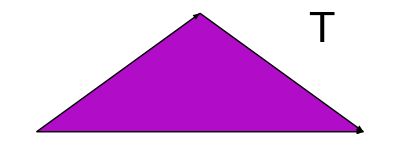

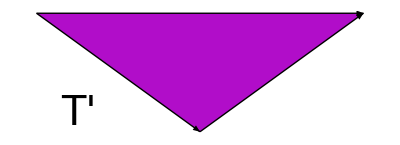

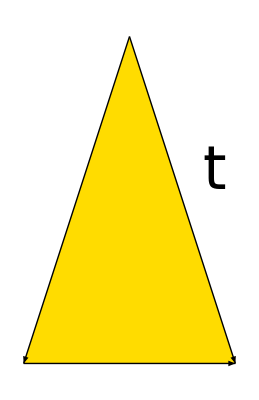

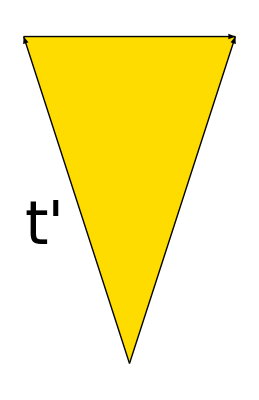

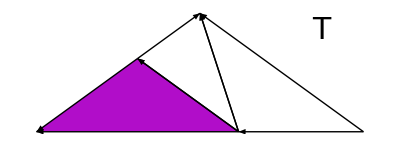
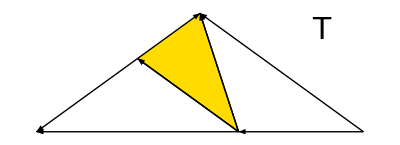
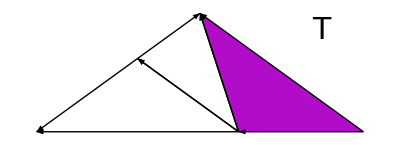

```mathematica
TR=Show[See@Inflate[{unitfat},0],ArrowEdges/@Inflate[{unitfat},0],Graphics[Text[Style["T",2*20, FontFamily->"CMU Serif"],{0.6,0.5}]]]

TL=Rotate[Show[See@Inflate[{Conj@unitfat},0],ArrowEdges/@Inflate[{Conj@unitfat},0],Graphics[Rotate[Text[Style["T'",2*20, FontFamily->"CMU Serif"],{-0.6,-0.5}],Pi]]],Pi]

tR=Show[See@Inflate[{unitskinny},0],ArrowEdges/@Inflate[{unitskinny},0],Graphics[Text[Style["t",2*30, FontFamily->"CMU Serif"],{0.4,0.9}]]]

tL=Rotate[Show[See@Inflate[{Conj@unitskinny},0],ArrowEdges/@Inflate[{Conj@unitskinny},0],Graphics[Rotate[Text[Style["t'",2*30, FontFamily->"CMU Serif"],{-0.4,-0.9}],Pi]]],Pi]

{TR1,TR2,TR3}=Table[Show[See@{Inflate[{unitfat},1][[i]]},ArrowEdges/@Inflate[{unitfat},1],Graphics[Text[Style["T",2*15, FontFamily->"CMU Serif"],{0.6,0.5}]]],{i,{1,2,3}}]

{tR1,tR2}=Table[Show[See@{Inflate[{unitskinny},1][[i]]},ArrowEdges/@Inflate[{unitskinny},1],Graphics[Text[Style["t",2*20, FontFamily->"CMU Serif"],{0.4,0.9}]]],{i,{1,2}}]

{TL1,TL2,TL3}=Table[Rotate[Show[See@{Inflate[{Conj@unitfat},1][[i]]},ArrowEdges/@Inflate[{Conj@unitfat},1],Graphics[Rotate[Text[Style["T'",2*15, FontFamily->"CMU Serif"],{-0.6,-0.5}],Pi]]],Pi],{i,{1,2,3}}]

{tL1,tL2}=Table[Rotate[Show[See@{Inflate[{Conj@unitskinny},1][[i]]},ArrowEdges/@Inflate[{Conj@unitskinny},1],Graphics[Rotate[Text[Style["t'",2*20, FontFamily->"CMU Serif"],{-0.4,-0.9}],Pi]]],Pi],{i,{1,2}}]
```

```mathematica
graphedgelabel:=Graphics[{Table[{Opacity[0.4-1/n],FaceForm[White],Disk[{0,0},1/n]},{n,1,50}],{Text[Style[#,40, FontFamily->"CMU Serif"]]}}]&
```

```mathematica
Graph[{Labeled[TR->TR3,graphedgelabel["ϵ"]],Labeled[TR->TL1,graphedgelabel["γ'"]],Labeled[TR->tR2,graphedgelabel["α"]]},
VertexShapeFunction->"Name",
VertexSize->0.5,
GraphStyle->"BasicBlack",ImagePadding->50,ImageSize->Large
]
Export["TRgraph.png",%,ImageResolution->300]
```

-Graphics-

TRgraph.png

```mathematica
Graph[{Labeled[TL->TL3,graphedgelabel["ϵ'"]],Labeled[TL->tL2,graphedgelabel["α'"]],Labeled[TL->TR1,graphedgelabel["γ"]]},
VertexShapeFunction->"Name",
VertexSize->0.6,
GraphStyle->"BasicBlack",ImagePadding->60,ImageSize->Large
]
Export["TLgraph.png",%,ImageResolution->300]
```

-Graphics-

TLgraph.png

```mathematica
Graph[{Labeled[tL->tL1,graphedgelabel["β'"]],Labeled[tL->TR2,graphedgelabel["δ"]]},
VertexShapeFunction->"Name",
VertexSize->0.7,
GraphStyle->"BasicBlack",ImagePadding->120,ImageSize->Large
]
Export["tslgraph.png",%,ImageResolution->300]
```

-Graphics-

tslgraph.png

```mathematica
Graph[{Labeled[tR->tR1,graphedgelabel["β"]],Labeled[tR->TL2,graphedgelabel["δ'"]]},
VertexShapeFunction->"Name",
VertexSize->0.7,
GraphStyle->"BasicBlack",ImagePadding->120,ImageSize->Large
]
Export["tsrgraph.png",%,ImageResolution->300]
```

-Graphics-

tsrgraph.png

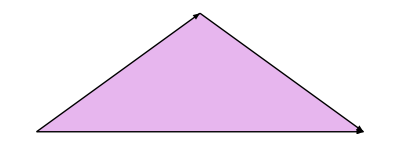

TFRob.png

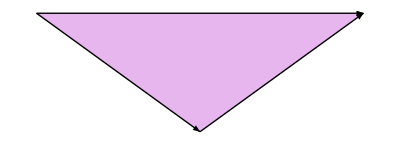

T'FRob.png

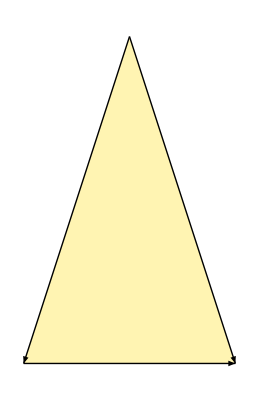

TSRob.png

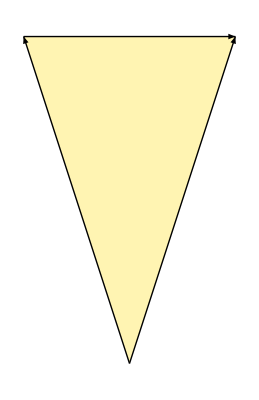

T'SRob.png

-Graphics-

-Graphics-

```mathematica
Show[SeeFaded[{unitfat}],ArrowEdges[unitfat]]
Export["TFRob.png",%,ImageResolution->300]
Rotate[Show[SeeFaded[{Conj@unitfat}],ArrowEdges[Conj@unitfat]],Pi]
Export["T'FRob.png",%,ImageResolution->300]
Show[SeeFaded[{unitskinny}],ArrowEdges[unitskinny]]
Export["TSRob.png",%,ImageResolution->300]
Rotate[Show[SeeFaded[{Conj@unitskinny}],ArrowEdges[Conj@unitskinny]],Pi]
Export["T'SRob.png",%,ImageResolution->300]
```

```mathematica
??See
```

Displays list of polygons as a graphic

See:=Graphics[{Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&

```mathematica
unitskinny
```

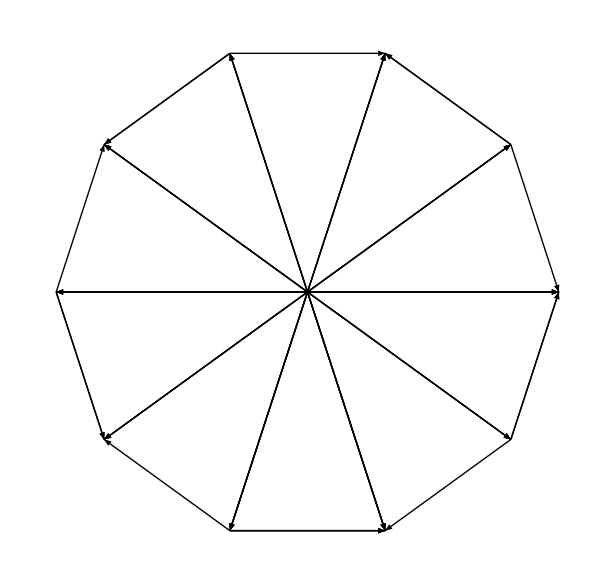

WedgeWheel.png

```mathematica
Show[Table[ArrowEdges@{Exp[i I Pi/5]*({0.5,-0.5,0.+1.5388417685876268 ⅈ}-(0.+1.5388417685876268 ⅈ)),"skinny"},{i,1,10,2}],Table[ArrowEdges@{Exp[i I 2Pi/5]*({-0.5,0.5,0.+1.5388417685876268 ⅈ}-(0.+1.5388417685876268 ⅈ)),"skinny"},{i,0,10}]]
Export["WedgeWheel.png",%,ImageResolution->300]
```

```mathematica
Show[Table[ArrowEdges@{Exp[i I Pi/5]*({0.5,-0.5,0.+1.5388417685876268 ⅈ}-(0.+1.5388417685876268 ⅈ)),"skinny"},{i,1,10,2}],Table[ArrowEdges@{Exp[i I 2Pi/5]*({-0.5,0.5,0.+1.5388417685876268 ⅈ}-(0.+1.5388417685876268 ⅈ)),"skinny"},{i,0,10}]]
```

```mathematica
unitfat
```

```mathematica
{{-0.8090169943749475,0.8090169943749475,1.1102230246251565*^-16+0.5877852522924732 ⅈ}-(1.1102230246251565*^-16+0.5877852522924732 ⅈ),"fat"}
```

```mathematica
{{-0.8090169943749476-0.5877852522924732 ⅈ,0.8090169943749473-0.5877852522924732 ⅈ,0.+0. ⅈ},"fat"}
```

{{-0.809017-0.587785 ⅈ,0.809017-0.587785 ⅈ,0.+0. ⅈ},fat}